# Expression of colored Δ_T noise

```mathematica
f1[G_,ω_,x_]:=1/(1+Exp[(G+ω*10)/(1+x/2)]);
f2[G_,ω_,x_]:=1/(1+Exp[(G+ω*10)/(1-x/2)]);
D1[ω_?NumericQ,x_?NumericQ]:=0.25NIntegrate[(f2[G,0,x]-f1[G,0,x])(f2[G,ω,x]-f1[G,ω,x]),{G,-∞,∞}]
```

# Fig. 2(a) of paper

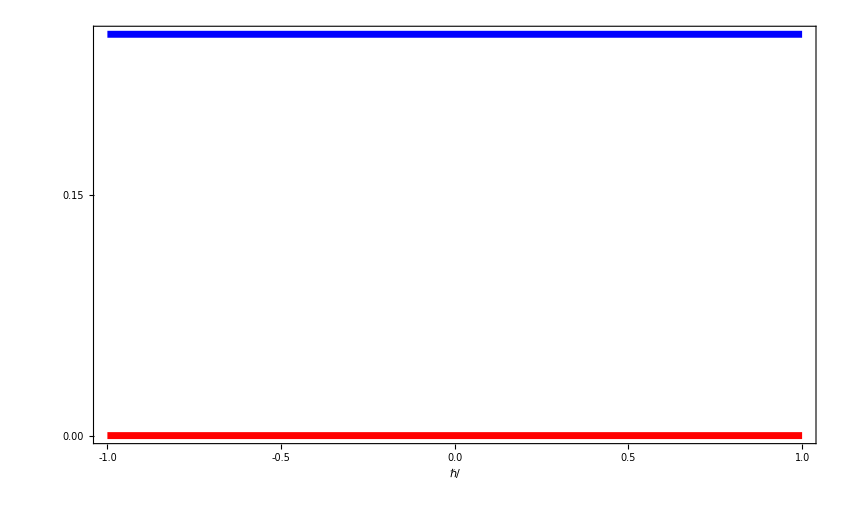

```mathematica
A1=Plot[{0,(1)0.5*0.5},{ω,-1,1},PlotRange->{{-1,1},{0.3,-0.02}},Exclusions->None,AxesOrigin->{0.0,-0.02},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.15,"0.15"},{0.30,"0.30"},{0,"0.00"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->850,Frame->True]
```

```mathematica
A2=Legended[Plot[{0,D1[ω,0.1]},{ω,-1,1},PlotRange->{{-1,1},{0.0006,-0.0003}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",55,Black],Style["",55,Black]},{Right,Top}],FrameLabel->{Style["ℏ/",55,Bold,Black],Style[Rotate["",270 Degree],55,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0003,"0.30"},{0,"0.00"},{-0.0003,"-0.30"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,55],ImageSize->1700,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.35,0.95}],Scaled[{0.35,0.95}],1.10],PlotRange->{0.2,0.3},PlotRangeClipping->False}],{Placed[Style["× 10^-3",55,Black],{{0.25,1.0}}]}]
```

-Graphics-

# Fig. 2(b) of paper

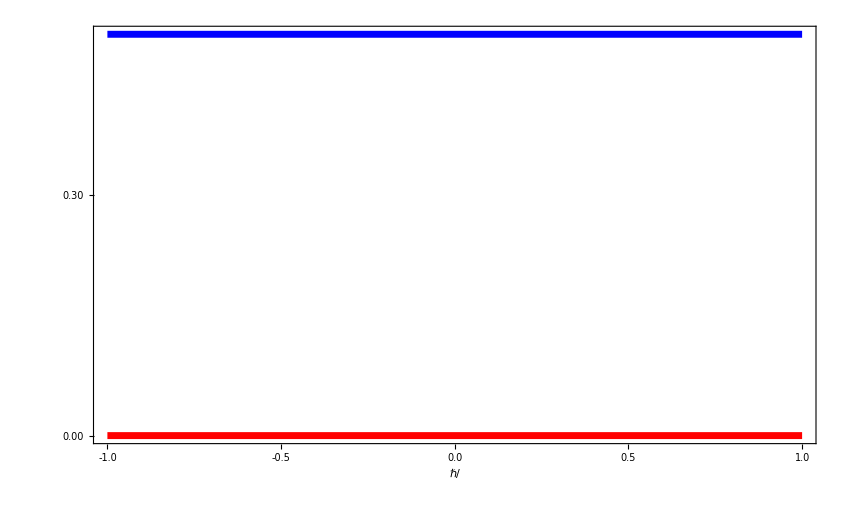

```mathematica
A1=Plot[{0,(2)0.5*0.5},{ω,-1,1},PlotRange->{{-1,1},{0.6,-0.02}},Exclusions->None,AxesOrigin->{0.0,-0.02},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.60,"0.60"},{0.30,"0.30"},{0,"0.00"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1.00,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->850,Frame->True]
```

```mathematica
A2=Legended[Plot[{0,2D1[ω,0.1]},{ω,-1,1},PlotRange->{{-1,1},{0.0012,-0.0006}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",55,Black],Style["",55,Black]},{Right,Top}],FrameLabel->{Style["ℏ/",55,Bold,Black],Style[Rotate["",270 Degree],55,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0012,"1.20"},{0.0006,"0.60"},{0,"0.00"},{-0.0006,"-0.60"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,55],ImageSize->1700,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.35,0.95}],Scaled[{0.35,0.95}],1.10],PlotRange->{0.2,0.3},PlotRangeClipping->False}],{Placed[Style["× 10^-3",55,Black],{{0.25,1.0}}]}]
```

-Graphics-

# Fig. 2(a) of Supplemental Material

```mathematica
A1=Legended[Plot[{0,D1[0,x],D1[0.5,x],D1[1,x]},{x,0,0.1},PlotRange->{{0,0.1},{0.0006,-0.00002}},Exclusions->None,AxesOrigin->{0.0,-0.00002},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45],Style["ℏ",45],Style["ℏ",45],Style["ℏ",45]},{Left,Top}],FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0003,"0.30"},{0,"0.00"}},None},{{{0.1,"0.10"},{0.05,"0.05"},{0,"0.00"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-

# Fig. 2(b) of Supplemental Material

```mathematica
A1=Legended[Plot[{0,2D1[0,x],2D1[0.5,x],2D1[1,x]},{x,0,0.1},PlotRange->{{0,0.1},{0.0012,-0.00002}},Exclusions->None,AxesOrigin->{0.0,-0.00002},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45],Style["ℏ",45],Style["ℏ",45],Style["ℏ",45]},{Left,Top}],FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0012,"1.20"},{0,"0.00"}},None},{{{0.1,"0.10"},{0.05,"0.05"},{0,"0.00"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-

# Fig. 3 of Supplemental Material

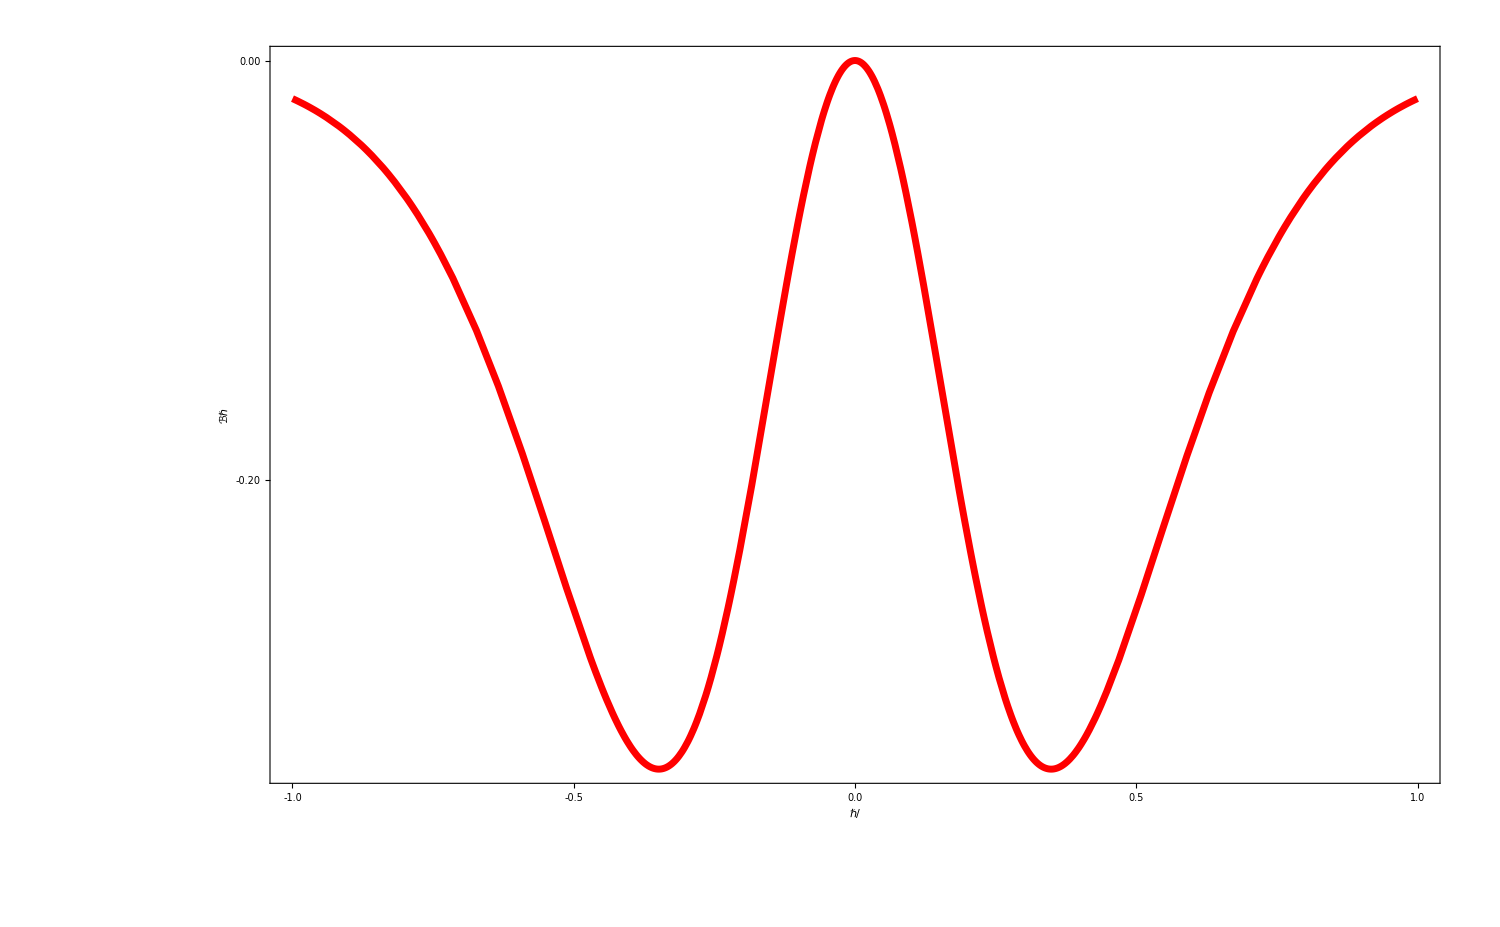

```mathematica
a=x*10;
A1=Plot[Exp[a]/(6(Exp[a]-1)^3)(2(π^2-E^a π^2+6 (-1+E^a) PolyLog[2,-E^-a]+6 (-1+E^a) PolyLog[2,-E^a]+6 PolyLog[3,-E^-a]+6 E^a PolyLog[3,-E^-a]-6 PolyLog[3,-E^a]-6 E^a PolyLog[3,-E^a])),{x,-1,1},PlotRange->{{-1,1},{0,0.3}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Blue,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",35,Bold,Black],Style[Rotate["𝒜",270 Degree],35,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.15,"0.15"},{0.3,"0.30"},{0,"0.00"}},None},{{{-1,"-1.0"},{-0.5,"-0.5"},{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},None}},FrameTicksStyle->Directive["Label",Black,35],ImageSize->750,Frame->True];
A2=Plot[Exp[a]/(6(Exp[a]-1)^3)((π^2+E^a π^2+6 Log[1+E^-a]-6 E^a Log[1+E^-a]-6 Log[1+E^a]+6 E^a Log[1+E^a]+6 (1+E^a) PolyLog[2,-E^-a]+6 (1+E^a) PolyLog[2,-E^a])*a ),{x,-1,1},PlotRange->{{-1,1},{0,-0.4}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["ℬℏ",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{-0.2,"-0.20"},{-0.4,"-0.40"},{0,"0.00"}},None},{{{-1,"-1.0"},{-0.5,"-0.5"},{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.25,0.95}],Scaled[{0.25,0.95}],0.95],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```